# Face genealogy

Facial images convey many important human characteristics, such as identity, gender, expression, age, and ethnicity. 
Representative examples including face recognition, facial expression recognition, age estimation, gender classification and ethnicity recognition.

The database used is the KinFaceW includes around 50% Caucasians, 40% Asians, 7% African Americans, and 3% others; 40% of the 150 images are father-son pairs, 22% are father-daughter, 13% are mother-son, and 26% are mother-daughter. Therefore, it has a wide spread distribution of facial characteristics which depend on race, gender, age, career, etc. 

Objective:
Identify the kinship using faces.

Using the pre trained neural network, categorize the faces according to the kinship.

Dataset:
- KinFaceW is derived from Labeled faces in the Wild project. 

Face images are collected from the internet, including some public figure face images as well as their parents’ or children’s face images. Face images are captured under uncontrolled environments in two datasets with no restriction in terms of pose, lighting, background, expression, age, ethnicity, and partial occlusion. The difference of KinFaceW-I and KinFaceW-II is that face images with a kin relation were acquired from different photos in KinFaceW-I and the same photo in KinFaceW-II in most cases.

There are four kin relations in two datasets: Father-Son (F-S), Father-Daughter (F-D), Mother-Son (M-S), and Mother-Daughter (M-D). In the KinFaceW-I dataset, there are 156, 134, 116, and 127 pairs of kinship images for these four relations. For the KinFaceW-II dataset, each relation contains 250 pairs of kinship images. For ease of use, we manually labeled the coordinates of the eyes position of each face image, and aligned and cropped facial region into 64x64 to remove background. The following figures show some cropped face images from KinFaceW-I and KinFaceW-II datasets, respectively.

## Import files

Dataset KinFaceW I

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-I/images/"];
```

```mathematica
ClearAll[fatherSon];
```

```mathematica
fatherSon=Import["father-son/fs*"];
fatherDaughter=Import["father-dau/fd*"];
motherSon=Import["mother-son/ms*"];
motherDaughter= Import["mother-dau/md*"];
```

```mathematica
Manipulate[ImageAssemble[#&/@{fatherSon[[i*2-1]],fatherSon[[i*2]]}],{i,1,Length[fatherSon]/2,1}]
```

```mathematica
Manipulate[ImageAssemble[#&/@{fatherDaughter[[i*2-1]],fatherDaughter[[i*2]]}],{i,1,Length[fatherDaughter]/2,1}]
```

```mathematica
Manipulate[ImageAssemble[#&/@{motherSon[[i*2-1]],motherSon[[i*2]]}],{i,1,Length[motherSon]/2,1}]
```

```mathematica
Manipulate[ImageAssemble[#&/@{motherDaughter[[i*2-1]],motherDaughter[[i*2]]}],{i,1,Length[motherDaughter]/2,1}]
```

# Functions

```mathematica
createCouples[ imgs_List ] := Partition[ imgs , 2 ] ;

fakeCouples[ imgs_List ] := Transpose[
								{RandomSample[Transpose[createCouples[imgs]][[1]]] , RandomSample[Transpose[createCouples[imgs]][[2]]]}];

                                                       
createClasses[ imgs_List, { n_Integer, m_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> "couples" ,
                                     #2 -> "fake couples"
                                    } & ,
                                    
                                   { Take[
                                          createCouples[ imgs ],
                                          {n, m}
                                          ],
                                     Take[
                                          fakeCouples[ imgs ],
                                          {n, m}
                                          ]
                                   }
                                 ]
                               ]; 
                               
                                                                                                                         
createClassesNeural[ imgs_List,{ n_Integer, m_Integer },{ j_Integer, k_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> 1 ,
                                     #2 -> 2
                                    } & ,
                                    
                                   { createCouples[Take[
                                           imgs ,
                                          {n, m}
                                          ]],
                                      fakeCouples[ Take[ imgs, {j,k}]]
                                   }
                                 ]
                               ];           
                               
 labelsNeural[ imgs_List , labels_List ]:= AssociationThread[ labels -> Transpose@Partition[imgs,2]];
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               
 associationNeural[ imgs_List,labels_List, category_String]:= Association[AppendTo[labelsNeural[imgs,labels],"Output"-> Table[category,Length[imgs]/2]]];
```

```mathematica
trainingSet = createClasses[fatherSon,{11,110}]
```

```mathematica
trainingSet = createClasses[fatherSon,{1,100},{101,200}]
```

```mathematica
validationSet = createClasses[fatherSon,{401,450},{451,500}];
```

```mathematica
testSet = createClasses[fatherSon,{201,300},{301,400}];
```

```mathematica
cl=Classify[
trainingSet, 
ValidationSet-> validationSet
 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,testSet]
```

ClassifierMeasurementsObject[…]

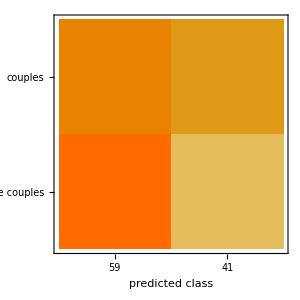

```mathematica
%["ConfusionMatrixPlot"]
```

```mathematica
trainingSet = createClasses[fatherSonDS1,{1,62},{63,124}];
```

```mathematica
validationSet = createClasses[fatherSonDS1,{249,280},{281,312}];
```

```mathematica
testSet = createClasses[fatherSonDS1,{125,186},{187,248}];
```

```mathematica
cl=Classify[
trainingSet, 
ValidationSet-> validationSet
 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,testSet]
```

ClassifierMeasurementsObject[…]

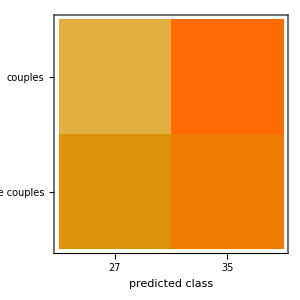

```mathematica
%["ConfusionMatrixPlot"]
```

# Feature extraction approach

## Neural network approach

Initialize the network

```mathematica
convP = Take[NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"], {1, "4b22"}];
fmodel2 = NetGraph[{convP, convP, CatenateLayer[], FlattenLayer[], LinearLayer[128], Ramp, LinearLayer[], SoftmaxLayer[]}, {NetPort["Parent"]->1->3, NetPort["Child"]->2->3, 3->4, 4->5, 5->6, 6->7->8}, "Output"->NetDecoder[{"Class",{"Parent","Not related"}}]];
net = NetInitialize[fmodel2]
```

NetGraph[<>]

Prepare data

```mathematica
realFatherSon=associationNeural[Flatten[createCouples[Take[fatherSon,300]]],{"Parent","Child"},"Parent"];

fakeFatherSon=associationNeural[Flatten[fakeCouples[Take[fatherSon,300]]],{"Parent","Child"},"Not related"];

dataFatherSon=Association[MapIndexed[First[{"Parent","Child","Output"}[[#2]]]->Flatten[#1] &,
Transpose[{Values[realFatherSon],Values[fakeFatherSon]}]]];
```

```mathematica
net
```

NetGraph[<>]

```mathematica
model = NetTrain[net,dataFatherSon , LearningRateMultipliers->{"1"->None, "2"-> None, _->1},ValidationSet->Scaled[0.2]]
```

NetGraph[<>]

```mathematica
model[testSet]
```

{Parent}

```mathematica
testSet=<|"Parent"->{ -Graphics-},"Child"->{-Graphics-},"Output"-> "Parent"|>
```

<|Parent→{-Graphics-},Child→{-Graphics-},Output→Parent|>

```mathematica
testSet
```

<|Parent→{-Graphics-},Child→{-Graphics-},Output→Parent|>

```mathematica
ClassifierMeasurements[model,testSet,"Accuracy"]
```

Proposal 1
Binary classification

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images

Partition::pdep: Depth 1 requested in object with dimensions {}.

MapThread::mptd: Object Partition[fatherDaughter,2] at position {2, 1} in MapThread[{#1→FatherDaughter}&,{Partition[fatherDaughter,2]}] has only 0 of required 1 dimensions.

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

```mathematica
averageColor[img_] := Total[Flatten[ImageData[img],1],{1}] / 
(Times @@ ImageDimensions[img])
```

```mathematica
FeatureExtraction[dataFatherSon[[1]][[1]]]
```

```mathematica
FacialFeatures[dataFatherSon[[1]][[1]],"NosePoints"]
```

```mathematica
dataFatherSon[[1]][[1]]
```

```mathematica
FacialFeatures[dataFatherSon[[5]]]
```

# Vectors ResNet

```mathematica
features=NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"][fatherSon];
```

```mathematica
features[[1]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Said/Github/Said_Summer2018/Project

```mathematica
Export["processedImagesResNet_101.mx",features,"MX"]
```

processedImagesResNet_101.mx

```mathematica
Export["images_classes_validationset.mx",validationSet,"MX"];
Export["images_classes_trainingset.mx",trainingSet,"MX"];
Export["images_classes_testset.mx",testSet,"MX"];
```

```mathematica
f=Import["processedImagesResNet_101.mx"];
```

```mathematica
f[[1]]
```

```mathematica
Map[RotateLeft[ # , 1 ]&,Partition[RotateLeft[ {1,2,3,4} , 1 ],2]]
```

{{3,2},{1,4}}

```mathematica
createCouples[
                                          RotateLeft[ imgs , 1 ]
                                         ]
```

```mathematica
f//Length
```

500

```mathematica
createClasses[f,{1,200}]
```

```mathematica
trainingSet = createClasses[f,{1,100}];
```

```mathematica
validationSet = createClasses[f,{101,150}];
```

```mathematica
testSet = createClasses[f,{151,200}];
```

couples

```mathematica
clvectores=Classify[
trainingSet, 
ValidationSet-> validationSet

 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[clvectores,testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
createClasses[f]
```

createClasses[{{0.036862,0.0338027,0.250632,0.,0.,0.0532649,0.655749,2.52846,0.941102,0.0670733,0.593426,2.68666,0.,5.56874,0.0382102,1.11091,2016,0.159244,0.000385965,0.,3.09961,0.237749,0.,3.23726,0.,0.000413366,4.14144,0.222531,1.08564,0.275688,3.93431,0.0109102,2.70382},498,{1}}]
 |  |  |  |

```mathematica
fa
```

```mathematica
points=DimensionReduce[features,2,Method-> "TSNE"]
```

```mathematica
Dimensions[points]
```

{500,2}

```mathematica
Graphics[MapThread[Inset[#1,#2,{0,0},0.5]&, {fatherSon,points}], ImageSize->Full, ImagePadding->25]
```

-Graphics-

```mathematica
FeatureNearest[fatherSon, -Graphics-, 5, 
 FeatureExtractor -> 
  NetModel["ResNet-101 Trained on Augmented Casia WebFace Data"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}